## Setup of full non-linear equations

### Geometry

```mathematica
Needs["EDCRGTCcode`"]
```

SetDelayed::write: Tag Classify in Classify[x_] is Protected.

Needs::nocont: Context EDCRGTCcode` was not created when Needs was evaluated.

```mathematica
gIN=DiagonalMatrix[{g'[r0]^2/Γ[r0],g[r0]^2,g[r0]^2 Sin[θ]^2}];
xIN={r0,θ,ϕ};
RGtensors[gIN,xIN]
```

gdd = (g'[r0]^2/Γ[r0] | 0 | 0
0 | g[r0]^2 | 0
0 | 0 | g[r0]^2 Sin[θ]^2)

LineElement = d[θ]^2 g[r0]^2+d[ϕ]^2 g[r0]^2 Sin[θ]^2+(d[r0]^2 g'[r0]^2)/Γ[r0]

gUU = (Γ[r0]/g'[r0]^2 | 0 | 0
0 | 1/g[r0]^2 | 0
0 | 0 | Csc[θ]^2/g[r0]^2)

gUU computed in 0. sec

Gamma computed in 0. sec

Riemann(dddd) computed in 0. sec

Riemann(Uddd) computed in 0. sec

Ricci computed in 0. sec

Weyl computed in 0. sec

Testing for 3-dim conformal flatness...

Conformally Flat

Einstein computed in 0. sec

All tasks completed in 0. seconds

```mathematica
(* Ricci scalar *)
ℛ=R//Together
```

-(2 (-g'[r0]+Γ[r0] g'[r0]+g[r0] Γ'[r0]))/(g[r0]^2 g'[r0])

```mathematica
(* Einstein Tensor *)
Edd=Rdd-1/2 R gdd//FullSimplify;
Edd//MatrixForm
```

(((-1+Γ[r0]) g'[r0]^2)/(g[r0]^2 Γ[r0]) | 0 | 0
0 | (g[r0] Γ'[r0])/(2 g'[r0]) | 0
0 | 0 | (g[r0] Sin[θ]^2 Γ'[r0])/(2 g'[r0]))

```mathematica
-Graphics-;
```

```mathematica
α=2;
f[ℛ_]:=1/α(ℛ-Rs)^α
EshelbyTarget=2 λ gUU.(f'[R]Rdd-1/2f[R]gdd)-2λ gUU.covD[covD[f'[R]]]+2λ gUU.gdd Laplacian[f'[R]]+Ws gUU.gdd//FullSimplify;
EshelbyTarget//MatrixForm
```

(Ws-(Rs^2 λ)/2+(2 λ (-1+Γ[r0]) (1+7 Γ[r0]))/g[r0]^4+(2 λ ((Rs-Rs Γ[r0]) g'[r0]^3+4 Γ[r0] Γ'[r0] g''[r0]+g'[r0] (Γ'[r0]^2-4 Γ[r0] Γ''[r0])))/(g[r0]^2 g'[r0]^3) | 0 | 0
0 | (((2 Ws-Rs^2 λ) g[r0]^4+4 λ (1+(6-7 Γ[r0]) Γ[r0])) g'[r0]^5-2 λ g[r0] (6+Rs g[r0]^2-14 Γ[r0]) g'[r0]^4 Γ'[r0]-24 λ g[r0]^3 Γ[r0] Γ'[r0] g''[r0]^2+4 λ g[r0]^3 g'[r0] (g''[r0] (Γ'[r0]^2+6 Γ[r0] Γ''[r0])+2 Γ[r0] Γ'[r0] g^(3)[r0])-4 λ g[r0]^3 g'[r0]^2 (Γ'[r0] Γ''[r0]+2 Γ[r0] Γ^(3)[r0]))/(2 g[r0]^4 g'[r0]^5) | 0
0 | 0 | (((2 Ws-Rs^2 λ) g[r0]^4+4 λ (1+(6-7 Γ[r0]) Γ[r0])) g'[r0]^5-2 λ g[r0] (6+Rs g[r0]^2-14 Γ[r0]) g'[r0]^4 Γ'[r0]-24 λ g[r0]^3 Γ[r0] Γ'[r0] g''[r0]^2+4 λ g[r0]^3 g'[r0] (g''[r0] (Γ'[r0]^2+6 Γ[r0] Γ''[r0])+2 Γ[r0] Γ'[r0] g^(3)[r0])-4 λ g[r0]^3 g'[r0]^2 (Γ'[r0] Γ''[r0]+2 Γ[r0] Γ^(3)[r0]))/(2 g[r0]^4 g'[r0]^5))

```mathematica
Clear[R];
r0=R;

$Assumptions={g[R]>0, R>0, ϵ>0, Γ[R]>0, g'[R]>0, Sin[θ]>0, Rs>0, γR[R]>0, γθ[R]>0, γθ'[R]>0, Jg>0, JgS>0, r[R]>0, r'[R]>0, B>0, μ>0, Rs!=0};
```

```mathematica
(* verify contracted Bianchi ∇_A (R^AB-1/2 R G^AB)=0 *)
covDiv[Raise[Rdd-1/2 ℛ gdd,1,2],{1,{2}}]
```

{0,0,0}

### Mechanics

```mathematica
(* legacy stuff *)
subP:={γR->Function[R, g'[R]/√Γ[R]],γθ->Function[R,g[R]/R ]}
M=gdd;
```

```mathematica
Ften=DiagonalMatrix[{r'[R],r[R]/R, r[R]/R}];
Gten=DiagonalMatrix[{γR[R],γθ[R],γθ[R]}];
Aten=Ften.Inverse[Gten];
Bten=Aten.Transpose[Aten];
I1=Tr[Transpose[Aten].Aten];
Id=IdentityMatrix[3];
```

```mathematica
W=μ/2(I1-3);
Tten=μ Bten -p[R] Id;
```

```mathematica
TRR:=Tten[[1,1]];
Tθθ:=Tten[[2,2]];
ΔT:=Tθθ-TRR
Ttemp:=DiagonalMatrix[{TR[R],TR[R]+ΔT, TR[R]+ΔT}]
```

```mathematica
W/.subP
```

1/2 μ (-3+(2 r[R]^2)/g[R]^2+(Γ[R] r'[R]^2)/g'[R]^2)

```mathematica
Bten==DiagonalMatrix[{1,R^2 ,R^2 Sin[θ]^2 }].Ften.Inverse[M].Transpose@Ften/.subP
```

True

```mathematica
Det[Aten]^2==Det[Bten]
```

True

```mathematica
ODEMEL=Det[Aten]==1/.subP
```

(r[R]^2 √Γ[R] r'[R])/(g[R]^2 g'[R])==1

```mathematica
ODEdivT= TR'[R]==(2r'[R])/r[R] ΔT/.First@Solve[ODEMEL, r'[R]]/.subP//FullSimplify (* stress balance div T = 0 *)
```

2 μ (-g[R]^6+r[R]^6) g'[R]==r[R]^7 √Γ[R] TR'[R]

```mathematica
Eshelby = W IdentityMatrix[3]-DiagonalMatrix[{TR[R], TR[R]+ΔT,  TR[R]+ΔT}]/.First@Solve[ODEMEL, r'[R]]/.subP//FullSimplify//FullSimplify
```

{{1/2 μ (-3+g[R]^4/r[R]^4+(2 r[R]^2)/g[R]^2)-TR[R],0,0},{0,-(3 μ)/2+(3 μ g[R]^4)/(2 r[R]^4)-TR[R],0},{0,0,-(3 μ)/2+(3 μ g[R]^4)/(2 r[R]^4)-TR[R]}}

```mathematica
Eshelby//MatrixForm
```

(1/2 μ (-3+g[R]^4/r[R]^4+(2 r[R]^2)/g[R]^2)-TR[R] | 0 | 0
0 | -(3 μ)/2+(3 μ g[R]^4)/(2 r[R]^4)-TR[R] | 0
0 | 0 | -(3 μ)/2+(3 μ g[R]^4)/(2 r[R]^4)-TR[R])

### Full non-linear equations

```mathematica
GrowthLaw=Thread[{0,0}==Diagonal[ EshelbyTarget-Eshelby+0 χ/3 (1-Det[Gten]/JgS)IdentityMatrix[3]][[1;;2]]]/.subP//FullSimplify
```

{1/2 (Rs^2 λ+μ (-3+g[R]^4/r[R]^4+(2 r[R]^2)/g[R]^2))==Ws+TR[R]+(2 λ (-1+Γ[R]) (1+7 Γ[R]))/g[R]^4+(2 λ ((Rs-Rs Γ[R]) g'[R]^3+4 Γ[R] Γ'[R] g''[R]+g'[R] (Γ'[R]^2-4 Γ[R] Γ''[R])))/(g[R]^2 g'[R]^3),(Rs^2 λ)/2+(3 μ g[R]^4)/(2 r[R]^4)+1/(g[R] g'[R]^5)λ (Rs g'[R]^4 Γ'[R]+12 Γ[R] Γ'[R] g''[R]^2-2 g'[R] (g''[R] (Γ'[R]^2+6 Γ[R] Γ''[R])+2 Γ[R] Γ'[R] g^(3)[R])+2 g'[R]^2 (Γ'[R] Γ''[R]+2 Γ[R] Γ^(3)[R]))==Ws+(3 μ)/2+TR[R]+(2 λ (1+(6-7 Γ[R]) Γ[R]+(g[R] (-3+7 Γ[R]) Γ'[R])/g'[R]))/g[R]^4}

```mathematica
DSolve[{ℛ==Rs, Γ[0]==1}, Γ[R], R]/.g[0]->0//FullSimplify
```

{{Γ[R]→1-1/6 Rs g[R]^2}}

```mathematica
EshelbyTarget/.Γ->Function[R, 1-1/6 Rs g[R]^2]//FullSimplify
```

{{Ws,0,0},{0,Ws,0},{0,0,Ws}}

```mathematica
(* these are the governing equations, notes Eq. (74) *)
ODEs={GrowthLaw,ODEdivT, ODEMEL}//Flatten//FullSimplify;
```

```mathematica
ODEs//MatrixForm
```

(1/2 (Rs^2 λ+μ (-3+g[R]^4/r[R]^4+(2 r[R]^2)/g[R]^2))==Ws+TR[R]+(2 λ (-1+Γ[R]) (1+7 Γ[R]))/g[R]^4+(2 λ ((Rs-Rs Γ[R]) g'[R]^3+4 Γ[R] Γ'[R] g''[R]+g'[R] (Γ'[R]^2-4 Γ[R] Γ''[R])))/(g[R]^2 g'[R]^3)
(Rs^2 λ)/2+(3 μ g[R]^4)/(2 r[R]^4)+(λ (Rs g'[R]^4 Γ'[R]+12 Γ[R] Γ'[R] g''[R]^2-2 g'[R] (g''[R] (Γ'[R]^2+6 Γ[R] Γ''[R])+2 Γ[R] Γ'[R] g^(3)[R])+2 g'[R]^2 (Γ'[R] Γ''[R]+2 Γ[R] Γ^(3)[R])))/(g[R] g'[R]^5)==Ws+(3 μ)/2+TR[R]+(2 λ (1+(6-7 Γ[R]) Γ[R]+(g[R] (-3+7 Γ[R]) Γ'[R])/g'[R]))/g[R]^4
2 μ (-g[R]^6+r[R]^6) g'[R]==r[R]^7 √Γ[R] TR'[R]
g[R]^2 g'[R]==r[R]^2 √Γ[R] r'[R])

```mathematica
subg={Γ->Function[R, Γ[g[R]]], r->Function[R, r[g[R]]],TR->Function[R, TR[g[R]]] } ;

subG[expr_]:=expr/.{Γ->Function[R, Γ[g[R]]], r->Function[R, r[g[R]]],TR->Function[R, TR[g[R]]] } /.g[R]->g

(* scaling gh = g √Rs or g = gh / √Rs , which means r'[g] = r'[gh] √Rs 
Since W = Wel + λ (R-Rs) clearly λ  = λh μ / Rs *)
subGh[expr_]:=Module[{t1, t2},
t1=expr/.{r'[g]->rh'[gh],TR'[g]->μ TRh'[gh] √(Rs /6), Γ'[g]->Γh'[gh] √(Rs /6),Γ''[g]->Γh''[gh]Rs /6,   Derivative[3][Γ][g]->Γh'''[gh](Rs /6)^(3/2)};
t2=t1/.{r[g]->rh[gh]/√(Rs /6), TR[g]->μ TRh[gh], Γ[g]->Γh[gh]};
t2/.{g->gh/√(Rs /6), λ->λh μ / (Rs /6)^2, Ws->wh μ}
]
```

```mathematica
FullSimplify[ℛ//subG]
%//subGh
```

-(2 (-1+Γ[g]+g Γ'[g]))/g^2

-(Rs (-1+Γh[gh]+gh Γh'[gh]))/(3 gh^2)

```mathematica
Det[gdd]
```

(g[R]^4 Sin[θ]^2 g'[R]^2)/Γ[R]

### full mechanical-geometric coupling

```mathematica
temp=subG[ODEs]//FullSimplify;
temp//MatrixForm
```

(1/2 (Rs^2 λ+μ (-3+g^4/r[g]^4+(2 r[g]^2)/g^2))==Ws-(2 λ)/g^4+(2 Rs λ)/g^2+TR[g]+(2 λ (7 Γ[g]^2+g^2 Γ'[g]^2-Γ[g] (6+g^2 Rs+4 g^2 Γ''[g])))/g^4
((3 g^5 μ)/r[g]^4+λ (g Rs^2+2 Γ'[g] (Rs+2 Γ''[g])+8 Γ[g] Γ^(3)[g]))/(2 g)==Ws+(3 μ)/2+TR[g]+(2 λ (1+(6-7 Γ[g]) Γ[g]+g (-3+7 Γ[g]) Γ'[g]))/g^4
2 g^6 μ+r[g]^7 √Γ[g] TR'[g]==2 μ r[g]^6
g^2==r[g]^2 √Γ[g] r'[g])

```mathematica
(* solve first growth law equation for Γ'' *)
Γ''[g]/.First@Solve[temp[[1]], Γ''[g]];

(* plug this result into second growth law equation to reduce its order *)
temp[[2]]/.Derivative[3][Γ][g]->D[%, g]//FullSimplify;

(* solve resulting equation for Γ''[g] *)
Γ''[g]/.First@Solve[%,Γ''[g]]//FullSimplify;

(* compare with Γ''[g] from first growth law equation *)
Γ''[g]/.First@Solve[temp[[1]], Γ''[g]]//FullSimplify;

(* compute the residual between the two *)
%-%%//FullSimplify;

(* check that the residual vanishes based on mechanics and incompressibility equations *)
%/.First@FullSimplify[Solve[temp[[3]]/.First@Solve[temp[[4]], Γ[g]], TR'[g]], Assumptions->{g>0, r[g]>0,r'[g]>0}]//FullSimplify
```

0

```mathematica
(* these are the two linearly independent equations *)
ODEsg=temp[[{1,3,4}]]

ODEsgh=subGh[ODEsg/.Rs->Rs k]//FullSimplify;
ODEsgh=%/.μ->1

TR[R]+ΔT/.subP/.Rs->Rs k;
Tθh[gh_]:=Evaluate[%/μ//subG//subGh//FullSimplify]
subG[Eshelby]//FullSimplify;
EshelbyR[gh_]:=Evaluate[1/μ subGh[%[[1,1]]]//FullSimplify]
EshelbyT[gh_]:=Evaluate[1/μ subGh[%%[[2,2]]]//FullSimplify]
```

{1/2 (Rs^2 λ+μ (-3+g^4/r[g]^4+(2 r[g]^2)/g^2))==Ws-(2 λ)/g^4+(2 Rs λ)/g^2+TR[g]+(2 λ (7 Γ[g]^2+g^2 Γ'[g]^2-Γ[g] (6+g^2 Rs+4 g^2 Γ''[g])))/g^4,2 g^6 μ+r[g]^7 √Γ[g] TR'[g]==2 μ r[g]^6,g^2==r[g]^2 √Γ[g] r'[g]}

{gh^7/rh[gh]+2 gh rh[gh]^5+1/gh rh[gh]^3 (-gh^4 (3+2 wh)+4 (1-3 gh^2 k)^2 λh-2 gh^4 TRh[gh]+4 λh (-7 Γh[gh]^2-gh^2 Γh'[gh]^2+Γh[gh] (6+6 gh^2 k+4 gh^2 Γh''[gh])))==0,2 gh^6+rh[gh]^7 √Γh[gh] TRh'[gh]==2 rh[gh]^6,gh^2==rh[gh]^2 √Γh[gh] rh'[gh]}

## Gh solver

### “global” functions

```mathematica
Clear@solGh
solGh[λhArg_,gBArg_?NumericQ,kArg_:1,whArg_:0.5, gAArg_:10^-2]:=NDSolve[{ODEsgh/.{λh->λhArg, k->kArg, wh->whArg}, rh[gAArg]==gAArg, TRh[gBArg]==0, Γh[gAArg]==1, 0==-2+6 gBArg^2 kArg+2 Γh[gBArg]+2 gBArg Γh'[gBArg]},{rh[gh],Γh[gh], TRh[gh], rh'[gh], TRh'[gh], Γh'[gh], Γh''[gh]},{gh,gAArg, gBArg }]
```

```mathematica
(* Derivation of the analytical JMPS 2024-like curve findgB[] :

DSolve[{-(-1+Γh[gh]+gh Γh'[gh])/(3 gh^2)==1, Γh[0]==1},Γh[gh], gh]
0==(1/2(gh^4/rh[gh]^4+2 rh[gh]^2/gh^2-3)-whArg)/.Γh[gh]->1-gh^2//FullSimplify
%/.rh[gh]->(3/2)^(1/3) ((-gh √k √(1-gh^2 k)+ArcSin[gh √k])/k^(3/2))^(1/3)
*)
```

```mathematica
(* Here's how that integral expression SgBAnalytical is derived: *)
(*  gh^2/(√Γh[gh])(1/2(gh^4/rh[gh]^4+2 rh[gh]^2/gh^2-3)-whArg)/.Γh->Function [gh, 1-k gh^2]/.rh[gh]->(3/2)^(1/3) ((-gh √k √(1-gh^2 k)+ArcSin[gh √k])/k^(3/2))^(1/3) *)

SgBAnalytical[ gBArg_,kArg_,whArg_, gAArg_]:=NIntegrate[(gh^2 (-whArg+1/2 (-3+(2 (2/3)^(1/3) gh^4)/(3 ((-gh √k √(1-gh^2 k)+ArcSin[gh √k])/k^(3/2))^(4/3))+(2^(1/3) 3^(2/3) ((-gh √k √(1-gh^2 k)+ArcSin[gh √k])/k^(3/2))^(2/3))/gh^2)))/(√(1-gh^2 k))/.k->kArg,{gh,gAArg,gBArg}]
```

```mathematica
(* Wel=W* at g=gB , equivalently dS/dg=0 *)
ℒparam[λhArg_,gBArg_,kArg_,whArg_, gAArg_]:=gh^2/(√Γh[gh])(1/2(gh^4/rh[gh]^4+2 rh[gh]^2/gh^2-3)-whArg)/.First@solGh[λhArg,gBArg,kArg,whArg, gAArg]/.gh->gBArg

(* R'(g)=0 at g=gB *)
RPrime[λhArg_,gBArg_,kArg_:1,whArg_:0.5, gAArg_:10^-2]:=-(2-2 Γh[gh]+gh^2 Γh''[gh])/(3 gh^3)/.First@solGh[λhArg,gBArg,kArg,whArg, gAArg]/.gh->gBArg

ℒparamIntegral[ghArg_, λhArg_,gBArg_,kArg_,whArg_, gAArg_]:=gh^2/(√Γh[gh])(1/2(gh^4/rh[gh]^4+2 rh[gh]^2/gh^2-3)-whArg+ 18(*kArg*) λhArg(-kArg-(-1+Γh[gh]+gh Γh'[gh])/(3 gh^2))^2)/.First@solGh[λhArg,gBArg,kArg,whArg, gAArg]/.gh->ghArg

integral[ λhArg_,gBArg_,kArg_,whArg_, gAArg_]:=NIntegrate[ℒparamIntegral[gh, λhArg,gBArg,kArg,whArg, gAArg],{gh,gAArg,gBArg}]

findgB[whArg_,k_:1]:=Re@gB/.FindRoot[3/2+whArg==((2/3)^(1/3) gh^4)/(3 ((-gh √k √(1-gh^2 k)+ArcSin[gh √k])/k^(3/2))^(4/3))+((3/2)^(2/3) ((-gh √k √(1-gh^2 k)+ArcSin[gh √k])/k^(3/2))^(2/3))/gh^2/.gh->gB, {gB, 1}]
findrB[whArg_,k_:1]:=(3/2)^(1/3) ((-gh √k √(1-gh^2 k)+ArcSin[gh √k])/k^(3/2))^(1/3)/.gh->findgB[whArg, k]

findgBNumerical[λhArg_,whArg_, kArg_,gAArg_, gRangeArg_]:=Module[{},
myWh=whArg;
Δrange=0.1;
gRange=Subdivide[findgB[myWh,kArg]-Δrange, findgB[myWh, kArg]+Δrange,7];
dat=Table[{gB,ℒparam[λhArg,gB,kArg,whArg, gAArg]},{gB,gRange}];
interp=Interpolation[dat, InterpolationOrder->1];
froot=gB/.FindRoot[interp[gB],{gB,Last@gRange}]
]

findrBNumerical[λhArg_,whArg_, kArg_,gAArg_, gRangeArg_]:=Module[{},
mygB=findgBNumerical[λhArg,whArg, kArg,gAArg, gRangeArg];
rh[gh]/.First@solGh[λhArg,mygB,kArg,whArg, gAArg]/.gh->mygB
]

gBmin=10^-3;
```

### Stress plots

```mathematica
getgB[sol_]:=Head[(Γh[gh]/.sol)[[1]]]["Domain"]//Last//Last

λh1=500;
λh2=0.01;
λh3=0.005;
myWh=0.02;


Print@First@AbsoluteTiming[gB1POS=findgBNumerical[λh1,myWh, 1,gBmin, "lololol"];
solλ1POS=solGh[λh1,gB1POS,1, myWh, gBmin]];
Print@First@AbsoluteTiming[gB2POS=findgBNumerical[λh2,myWh, 1,gBmin, "lololol"];
solλ2POS=solGh[λh2,gB2POS,1, myWh, gBmin]];
Print@First@AbsoluteTiming[gB3POS=findgBNumerical[λh3,myWh, 1,gBmin, "lololol"];
solλ3POS=solGh[λh3,gB3POS,1, myWh, gBmin]];


Print@First@AbsoluteTiming[gB1NEG=findgBNumerical[λh1,myWh, -1,gBmin, "lololol"];solλ1NEG=solGh[λh1,gB1NEG,-1, myWh, gBmin]];
Print@First@AbsoluteTiming[gB2NEG=findgBNumerical[λh2,myWh, -1,gBmin, "lololol"];solλ2NEG=solGh[λh2,gB2NEG,-1, myWh, gBmin]];
Print@First@AbsoluteTiming[gB3NEG=findgBNumerical[λh3,myWh, -1,gBmin, "lololol"];solλ3NEG=solGh[λh3,gB3NEG,-1, myWh, gBmin]];
```

3.14609

2.79121

2.70131

3.423

3.86184

4.73494

```mathematica
bs=15;
is=300;
th=0.01;
ar=0.7;
SetOptions[{Plot}, PlotTheme->"Scientific", FrameStyle->Black, BaseStyle->bs,  PlotStyle->Thickness[th], ImageSize->is];
LL=LineLegend[{Directive[Thickness[th], RGBColor[0.9, 0.36, 0.054]],Directive[Thickness[th], RGBColor[0.365248, 0.427802, 0.758297]], Directive[Thickness[th], RGBColor[0.285821, 0.56, 0.450773]]},{"λ̂ = "<>ToString[λh1],"λ̂ = "<>ToString[λh2],"λ̂ = "<>ToString[λh3]}];


Clear@MakePlot
MakePlot[quantity_,legendPos_:{Left, Top}, pos_:{{1,0.5},{1.2,0.5}}, title_:"my title", prange_:All, pPoints_:Automatic]:=Module[{P1pos, P2pos, P3pos, P1neg, P2neg, P3neg, GP},

GP=Graphics[{Black,  Dashed, Line[{{1,0},{1,secondGPcoordinate}}]}];


P1pos=Plot[quantity/.λh->λh1/.solλ1POS,{gh, gBmin, gB1POS}, PlotStyle->Directive[RGBColor[0.9, 0.36, 0.054], Thickness[1.5 th] ], PlotLegends->Placed[LL,legendPos], PlotPoints->pPoints];
P2pos=Plot[quantity/.λh->λh2/.solλ2POS,{gh, gBmin,  gB2POS}, PlotStyle->Directive[RGBColor[0.365248, 0.427802, 0.758297], Thickness[1 th]], PlotPoints->pPoints]; 
P3pos=Plot[quantity/.λh->λh3/.solλ3POS,{gh, gBmin,  gB3POS}, PlotStyle->Directive[RGBColor[0.285821, 0.56, 0.450773], Thickness[0.76th]], PlotPoints->pPoints]; 
PlotPOS=Show[P1pos, P2pos, P3pos, FrameLabel->{"dimensionless compatible metric ĝ=g√((ℛ^*)_+)" ,None}, AspectRatio->1, Epilog->{Inset[Style["k = 1", FontFamily->"Times"],pos[[1]]],Inset[Style["k = -1", FontFamily->"Times"],pos[[2]]]}, PlotLabel->title];

P1neg=Plot[quantity/.λh->λh1/.solλ1NEG,{gh, gBmin, gB1NEG},PlotStyle->Directive[RGBColor[0.9, 0.36, 0.054], Thickness[th] ], PlotPoints->pPoints]; 
P2neg=Plot[quantity/.λh->λh2/.solλ2NEG,{gh, gBmin, gB2NEG},PlotStyle->Directive[RGBColor[0.365248, 0.427802, 0.758297], Thickness[th]], PlotPoints->pPoints]; 
P3neg=Plot[quantity/.λh->λh3/.solλ3NEG,{gh, gBmin, gB3NEG},PlotStyle->Directive[RGBColor[0.285821, 0.56, 0.450773], Thickness[th]], PlotPoints->pPoints];  
PlotNEG=Show[P1neg, P2neg, P3neg];

temp=Show[{PlotPOS, PlotNEG}, PlotRange->prange, FrameStyle->Black];
temp
]
```

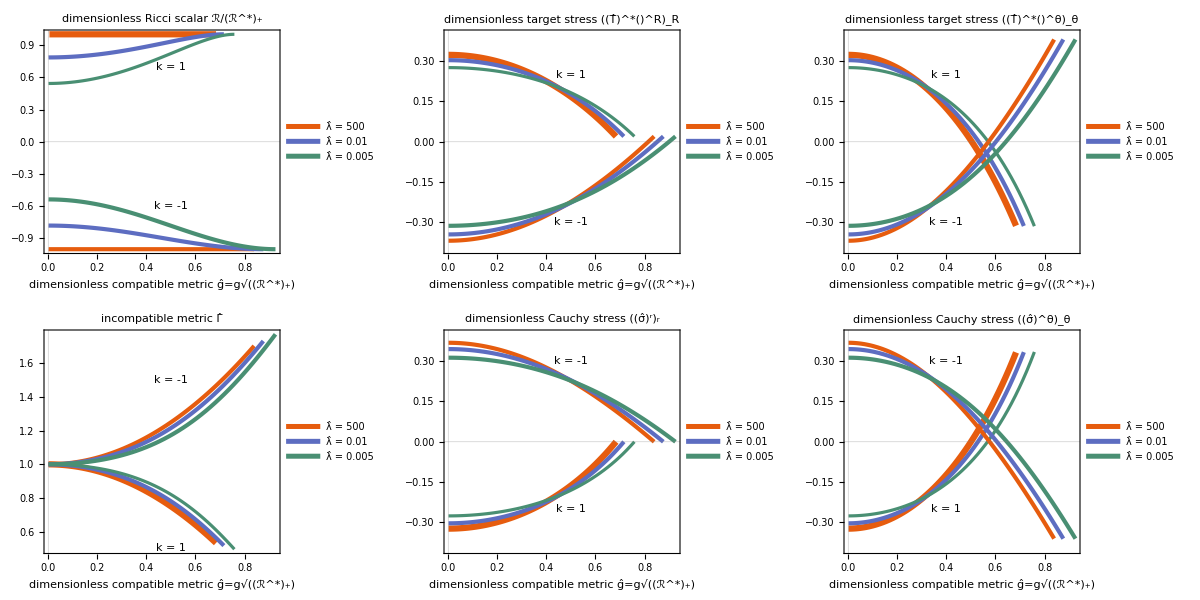

```mathematica
stressRange={All,{-0.4,0.4}};
MPℛ=MakePlot[-( (-1+Γh[gh]+gh Γh'[gh])/(3 gh^2)),{Right, Center},{{0.5,0.7},{0.5,-0.6}},"dimensionless Ricci scalar ℛ/(ℛ^*)_+",All];
MPTstarRR=MakePlot[EshelbyR[gh],{Left, Center},{{0.5,0.25},{0.5,-0.3}},"dimensionless target stress ((T̂)^*()^R)_R",stressRange];
MPTstarθθ=MakePlot[EshelbyT[gh],{Left,Center},{{0.4,0.25},{0.4,-0.3}},"dimensionless target stress ((T̂)^*()^θ)_θ",stressRange];
MPΓ=MakePlot[Γh[gh],{Left, Top},{{0.5,0.5},{0.5,1.5}}, "incompatible metric Γ̂",All];
MPσrr=MakePlot[TRh[gh],{Left,Center},{{0.5,-0.25},{0.5,0.3}},"dimensionless Cauchy stress ((σ̂)^r)_r",stressRange];
MPσθθ=MakePlot[Tθh[gh],{Left,Center},{{0.4,-0.25},{0.4,0.3}},"dimensionless Cauchy stress ((σ̂)^θ)_θ",stressRange];

GridBulk=Grid[{
{MPℛ,MPTstarRR,MPTstarθθ},
{MPΓ,MPσrr,MPσθθ}
}, Spacings->{3, 3}]
```

### Size functionals

```mathematica
gRange=Subdivide[0.2, 0.90, 10];

AbsoluteTiming[dat1POS=Table[{gB,integral[λh1,gB,1,myWh,gBmin]},{gB,gRange}];
dat2POS=Table[{gB,integral[ λh2,gB,1,myWh,gBmin]},{gB,gRange}];
dat3POS=Table[{gB,integral[ λh3,gB,1,myWh,gBmin]},{gB,gRange}];]
```

{36.8416,Null}

```mathematica
bs
```

15

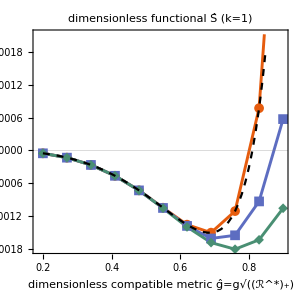

```mathematica
th=0.007;
is=300;
ar=1;
LPFunctionalPOS=ListPlot[{dat1POS, dat2POS, dat3POS}, Joined->True,PlotMarkers->{Automatic,10},ImageSize->is,PlotTheme->"Scientific",BaseStyle->bs,AspectRatio->ar,FrameLabel->{"dimensionless compatible metric ĝ=g√((ℛ^*)_+)" ,None}, FrameStyle->Black,  PlotLegends->Placed[LL,{Center, Top}], PlotStyle->{Directive[Thickness[th],RGBColor[0.9, 0.36, 0.054]],Directive[Thickness[th],RGBColor[0.365248, 0.427802, 0.758297]],Directive[Thickness[th],RGBColor[0.285821, 0.56, 0.450773]] }, PlotRange->{All, Automatic}, PlotLabel->"dimensionless functional Ŝ  (k=1)"];
gRange=Range[0.2, 0.90, 0.01];
ListPlot[{#,SgBAnalytical[ #,1,myWh, gBmin]}&/@gRange,Joined->True, PlotStyle->Directive[Black, Dashed], PlotLegends->Placed[{"λ̂ → ∞"},{Center,Top}], PlotTheme->"Scientific"];
LPFunctionalPOS=Show[LPFunctionalPOS, %]
```

```mathematica
gRange=Subdivide[0.4, 0.99, 10];
AbsoluteTiming[dat1NEG=Table[{gB,integral[λh1,gB,-1,myWh,gBmin]},{gB,gRange}];
dat2NEG=Table[{gB,integral[ λh2,gB,-1,myWh,gBmin]},{gB,gRange}];
dat3NEG=Table[{gB,integral[ λh3,gB,-1,myWh,gBmin]},{gB,gRange}];]
```

{38.9105,Null}

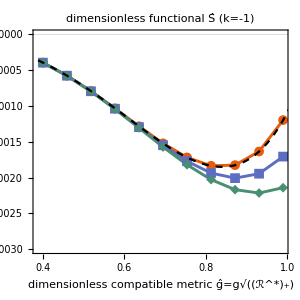

```mathematica
LPFunctionalNEG=ListPlot[{dat1NEG, dat2NEG, dat3NEG}, Joined->True,PlotMarkers->{Automatic,10},ImageSize->is,PlotTheme->"Scientific",BaseStyle->bs,AspectRatio->ar,FrameLabel->{"dimensionless compatible metric ĝ=g√((ℛ^*)_+)" ,None}, FrameStyle->Black,  PlotLegends->Placed[LL,{Left,Bottom}], PlotStyle->{Directive[Thickness[th],RGBColor[0.9, 0.36, 0.054]],Directive[Thickness[th],RGBColor[0.365248, 0.427802, 0.758297]],Directive[Thickness[th],RGBColor[0.285821, 0.56, 0.450773]] }, PlotRange->{Automatic,{-0.003,Automatic}}, PlotLabel->"dimensionless functional Ŝ  (k=-1)"];

gRange=Range[0.2, 1.1, 0.01];
ListPlot[{#,SgBAnalytical[ #,-1,myWh, gBmin]}&/@gRange,Joined->True, PlotStyle->Directive[Black, Dashed], PlotLegends->Placed[{"λ̂ → ∞"},{Left,Bottom}], PlotTheme->"Scientific"];
LPFunctionalNEG=Show[LPFunctionalNEG, %]
```

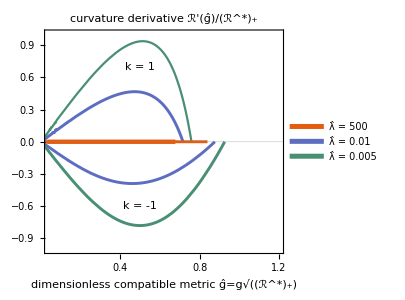

```mathematica
LPRprime=MakePlot[-(2-2 Γh[gh]+gh^2 Γh''[gh])/(3 gh^3) ,{Right, Top},{{0.5,0.7},{0.5,-0.6}},"curvature derivative ℛ'(ĝ)/(ℛ^*)_+",{{0.04,1.2},{-1,1}}, 4]
```

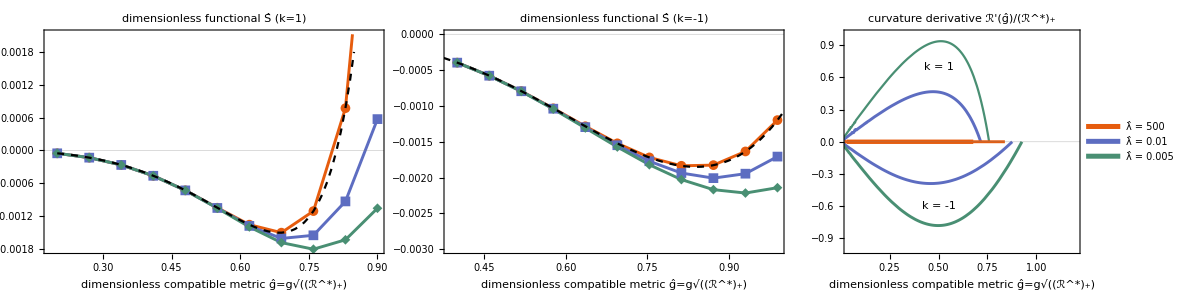

```mathematica
Grid[{{LPFunctionalPOS,LPFunctionalNEG, LPRprime}}, Spacings->{4, 1}]
```

### Size plots

```mathematica
whList=Table[2 10^i,{i, -4, -2, 0.25}]//N;

AbsoluteTiming[dat1POS={#, findrBNumerical[λh1,#, 1,gBmin, gRange]}&/@whList;]
AbsoluteTiming[dat2POS={#, findrBNumerical[λh2,#, 1,gBmin, gRange]}&/@whList;]
AbsoluteTiming[dat3POS={#, findrBNumerical[λh3,#, 1,gBmin, gRange]}&/@whList;]
AbsoluteTiming[dat1NEG={#, findrBNumerical[λh1,#, -1,gBmin, gRange]}&/@whList;]
AbsoluteTiming[dat2NEG={#, findrBNumerical[λh2,#, -1,gBmin, gRange]}&/@whList;]
AbsoluteTiming[dat3NEG={#, findrBNumerical[λh3,#, -1,gBmin, gRange]}&/@whList;]
```

{30.899,Null}

{39.4662,Null}

{39.8375,Null}

{36.6179,Null}

{37.636,Null}

{37.4397,Null}

```mathematica
whListLarge=Table[10^i,{i, -4, -0, 0.1}]//N;
datTruePos={#,findrB[#,1]}&/@whListLarge;
datTrueNeg={#,findrB[#,-1]}&/@whListLarge;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

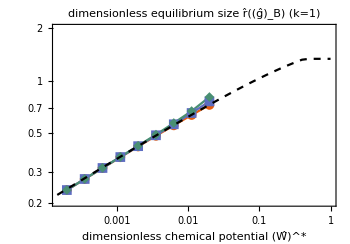

```mathematica
prange={{1.5 10^-4,10 10^-1},{0.2,2}};
ar=0.7;
is=350;
ps=0.02;
LPSizePOS=ListLogLogPlot[{dat1POS, dat2POS, dat3POS} ,Joined->True,PlotMarkers->{Automatic,10},ImageSize->is,PlotTheme->"Scientific",BaseStyle->bs,AspectRatio->ar,FrameLabel->{"dimensionless chemical potential (Ŵ)^*" ,None}, FrameStyle->Black,  PlotLegends->Placed[LL,{Right,Bottom}], PlotStyle->{Directive[PointSize[ps],RGBColor[0.9, 0.36, 0.054]],Directive[PointSize[ps],RGBColor[0.365248, 0.427802, 0.758297]],Directive[PointSize[ps],RGBColor[0.285821, 0.56, 0.450773]] }, PlotRange->prange, PlotLabel->"dimensionless equilibrium size r̂((ĝ)_B)  (k=1)"];

ListLogLogPlot[datTruePos, Joined->True, PlotStyle->Directive[Black, Dashed], PlotLegends->Placed[{"λ̂ → ∞"},{Right,Bottom}], PlotTheme->"Scientific"];
LPSizePOS=Show[LPSizePOS, %]
```

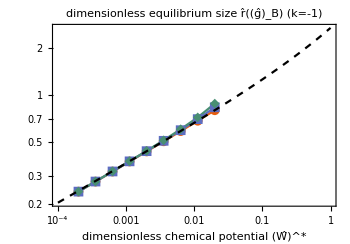

```mathematica
LPSizeNEG=ListLogLogPlot[{dat1NEG, dat2NEG, dat3NEG} ,Joined->True,PlotMarkers->{Automatic,10},ImageSize->is,PlotTheme->"Scientific",BaseStyle->bs,AspectRatio->ar,FrameLabel->{"dimensionless chemical potential (Ŵ)^*" ,None}, FrameStyle->Black,  PlotLegends->Placed[LL,{Right,Bottom}], PlotStyle->{Directive[PointSize[ps],RGBColor[0.9, 0.36, 0.054]],Directive[PointSize[ps],RGBColor[0.365248, 0.427802, 0.758297]],Directive[PointSize[ps],RGBColor[0.285821, 0.56, 0.450773]] }, PlotRange->prange, PlotLabel->"dimensionless equilibrium size r̂((ĝ)_B)  (k=-1)"];

ListLogLogPlot[datTrueNeg, Joined->True, PlotStyle->Directive[Black, Dashed], PlotLegends->Placed[{"λ̂ → ∞"},{Right,Bottom}], PlotTheme->"Scientific"];
LPSizeNEG=Show[LPSizeNEG, %, PlotRange->All]
```

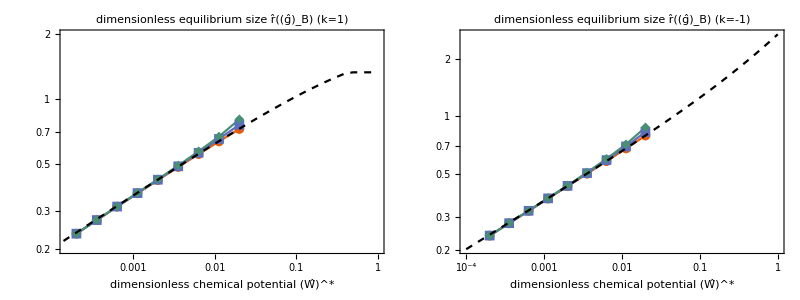

```mathematica
GridSize=Grid[{{LPSizePOS,LPSizeNEG}}, Spacings->{4, 1}]
```

## JMPS limit

In the limit λh->∞, only the bracket which prefactors λh survives:

```mathematica
First[ODEsgh]//Expand;
Collect[%,λh]/.λh->Highlighted[λh]
```

gh^7/rh[gh]-3 gh^3 rh[gh]^3-2 gh^3 wh rh[gh]^3+2 gh rh[gh]^5-2 gh^3 rh[gh]^3 TRh[gh]+λh ((4 rh[gh]^3)/gh-24 gh k rh[gh]^3+36 gh^3 k^2 rh[gh]^3+(24 rh[gh]^3 Γh[gh])/gh+24 gh k rh[gh]^3 Γh[gh]-(28 rh[gh]^3 Γh[gh]^2)/gh-4 gh rh[gh]^3 Γh'[gh]^2+16 gh rh[gh]^3 Γh[gh] Γh''[gh])==0

```mathematica
ODEsghJMPS=0==(4 rh[gh]^3)/gh-24 gh k rh[gh]^3+36 gh^3 k^2 rh[gh]^3+(24 rh[gh]^3 Γh[gh])/gh+24 gh k rh[gh]^3 Γh[gh]-(28 rh[gh]^3 Γh[gh]^2)/gh-4 gh rh[gh]^3 Γh'[gh]^2+16 gh rh[gh]^3 Γh[gh] Γh''[gh]//FullSimplify
```

(rh[gh] ((1-3 gh^2 k)^2-7 Γh[gh]^2-gh^2 Γh'[gh]^2+Γh[gh] (6+6 gh^2 k+4 gh^2 Γh''[gh])))/gh==0

```mathematica
ODEsghJMPS/.Γh->Function[gh, 1-k gh^2]//FullSimplify
```

True

```mathematica
Γh''[gh]/.First@Solve[ODEsghJMPS, Γh''[gh]]//FullSimplify;
%[[4]]
```

-(1-3 gh^2 k)^2+Γh[gh] (-6-6 gh^2 k+7 Γh[gh])+gh^2 Γh'[gh]^2